```mathematica
SetDirectory[NotebookDirectory[]];
```

sigma mass (polynomial fit)

```mathematica
Tdata=  Flatten[Import["./muB/muB560/TMeV.dat"]];
```

```mathematica
mSigmamuB560data=Flatten[Import["./muB/muB560/mSigma.dat"]];
```

```mathematica
mPionmuB560data=Flatten[Import["./muB/muB560/mPion.dat"]];
```

```mathematica
TtomSigmamuB560=Table[{Tdata[[i]],mSigmamuB560data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB560=Table[{Tdata[[i]],mPionmuB560data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB560=Table[{Tdata[[i]],mPionmuB560data[[i]]-mSigmamuB560data[[i]]},{i,1,Length[Tdata]}];
```

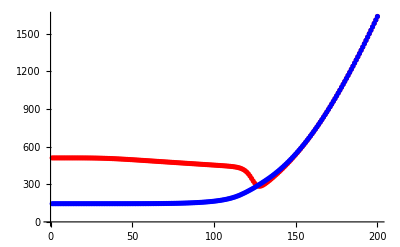

```mathematica
Show[ListPlot[TtomSigmamuB560,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB560,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

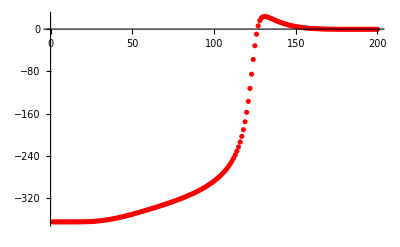

```mathematica
Show[ListPlot[mdiffmuB560,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB560=FindMaximum[Interpolation[mdiffmuB560][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB560=T/.FindMaximum[Interpolation[mdiffmuB560][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB560=FindMinimum[Interpolation[TtomSigmamuB560][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB560=T/.FindMinimum[Interpolation[TtomSigmamuB560][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB560=Interpolation[TtomPionmuB560][T]-Interpolation[TtomSigmamuB560][T]/.{T-> TmSigmaMinmuB560};
```

```mathematica
mSigmamuB570data=Flatten[Import["./muB/muB570/mSigma.dat"]];
```

```mathematica
mPionmuB570data=Flatten[Import["./muB/muB570/mPion.dat"]];
```

```mathematica
TtomSigmamuB570=Table[{Tdata[[i]],mSigmamuB570data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB570=Table[{Tdata[[i]],mPionmuB570data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB570=Table[{Tdata[[i]],mPionmuB570data[[i]]-mSigmamuB570data[[i]]},{i,1,Length[Tdata]}];
```

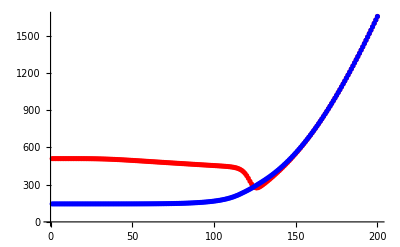

```mathematica
Show[ListPlot[TtomSigmamuB570,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB570,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

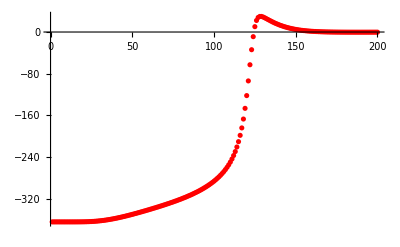

```mathematica
Show[ListPlot[mdiffmuB570,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB570=FindMaximum[Interpolation[mdiffmuB570][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB570=T/.FindMaximum[Interpolation[mdiffmuB570][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB570=FindMinimum[Interpolation[TtomSigmamuB570][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB570=T/.FindMinimum[Interpolation[TtomSigmamuB570][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB570=Interpolation[TtomPionmuB570][T]-Interpolation[TtomSigmamuB570][T]/.{T-> TmSigmaMinmuB570};
```

```mathematica
mSigmamuB580data=Flatten[Import["./muB/muB580/mSigma.dat"]];
```

```mathematica
mPionmuB580data=Flatten[Import["./muB/muB580/mPion.dat"]];
```

```mathematica
TtomSigmamuB580=Table[{Tdata[[i]],mSigmamuB580data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB580=Table[{Tdata[[i]],mPionmuB580data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB580=Table[{Tdata[[i]],mPionmuB580data[[i]]-mSigmamuB580data[[i]]},{i,1,Length[Tdata]}];
```

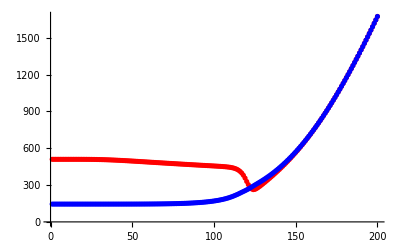

```mathematica
Show[ListPlot[TtomSigmamuB580,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB580,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

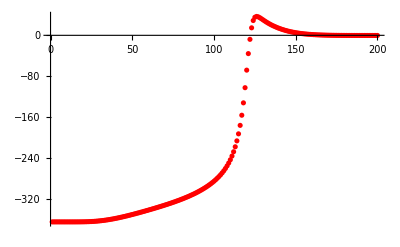

```mathematica
Show[ListPlot[mdiffmuB580,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB580=FindMaximum[Interpolation[mdiffmuB580][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB580=T/.FindMaximum[Interpolation[mdiffmuB580][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB580=FindMinimum[Interpolation[TtomSigmamuB580][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB580=T/.FindMinimum[Interpolation[TtomSigmamuB580][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB580=Interpolation[TtomPionmuB580][T]-Interpolation[TtomSigmamuB580][T]/.{T-> TmSigmaMinmuB580};
```

```mathematica
mSigmamuB590data=Flatten[Import["./muB/muB590/mSigma.dat"]];
```

```mathematica
mPionmuB590data=Flatten[Import["./muB/muB590/mPion.dat"]];
```

```mathematica
TtomSigmamuB590=Table[{Tdata[[i]],mSigmamuB590data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB590=Table[{Tdata[[i]],mPionmuB590data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB590=Table[{Tdata[[i]],mPionmuB590data[[i]]-mSigmamuB590data[[i]]},{i,1,Length[Tdata]}];
```

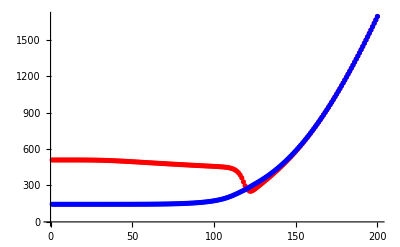

```mathematica
Show[ListPlot[TtomSigmamuB590,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB590,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

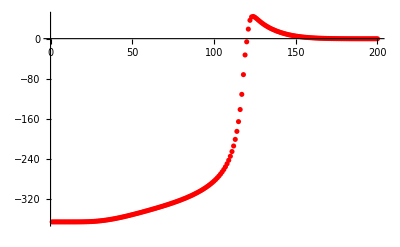

```mathematica
Show[ListPlot[mdiffmuB590,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB590=FindMaximum[Interpolation[mdiffmuB590][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB590=T/.FindMaximum[Interpolation[mdiffmuB590][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB590=FindMinimum[Interpolation[TtomSigmamuB590][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB590=T/.FindMinimum[Interpolation[TtomSigmamuB590][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB590=Interpolation[TtomPionmuB590][T]-Interpolation[TtomSigmamuB590][T]/.{T-> TmSigmaMinmuB590};
```

```mathematica
mSigmamuB590d5data=Flatten[Import["./muB/muB590d5/mSigma.dat"]];
```

```mathematica
mPionmuB590d5data=Flatten[Import["./muB/muB590d5/mPion.dat"]];
```

```mathematica
TtomSigmamuB590d5=Table[{Tdata[[i]],mSigmamuB590d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB590d5=Table[{Tdata[[i]],mPionmuB590d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB590d5=Table[{Tdata[[i]],mPionmuB590d5data[[i]]-mSigmamuB590d5data[[i]]},{i,1,Length[Tdata]}];
```

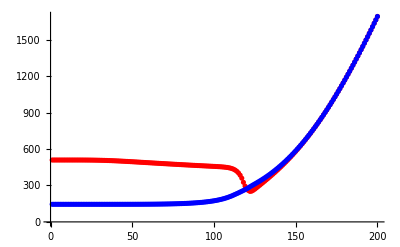

```mathematica
Show[ListPlot[TtomSigmamuB590d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB590d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

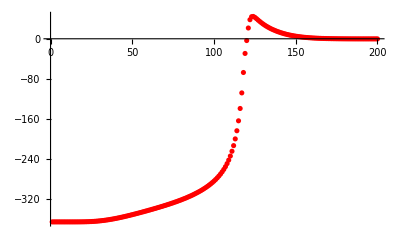

```mathematica
Show[ListPlot[mdiffmuB590d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB590d5=FindMaximum[Interpolation[mdiffmuB590d5][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB590d5=T/.FindMaximum[Interpolation[mdiffmuB590d5][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB590d5=FindMinimum[Interpolation[TtomSigmamuB590d5][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB590d5=T/.FindMinimum[Interpolation[TtomSigmamuB590d5][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB590d5=Interpolation[TtomPionmuB590d5][T]-Interpolation[TtomSigmamuB590d5][T]/.{T-> TmSigmaMinmuB590d5};
```

```mathematica
mSigmamuB591data=Flatten[Import["./muB/muB591/mSigma.dat"]];
```

```mathematica
mPionmuB591data=Flatten[Import["./muB/muB591/mPion.dat"]];
```

```mathematica
TtomSigmamuB591=Table[{Tdata[[i]],mSigmamuB591data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591=Table[{Tdata[[i]],mPionmuB591data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591=Table[{Tdata[[i]],mPionmuB591data[[i]]-mSigmamuB591data[[i]]},{i,1,Length[Tdata]}];
```

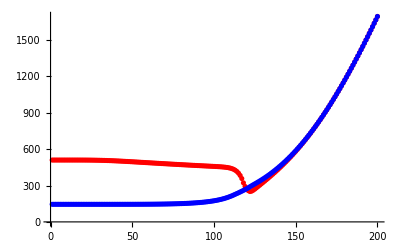

```mathematica
Show[ListPlot[TtomSigmamuB591,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

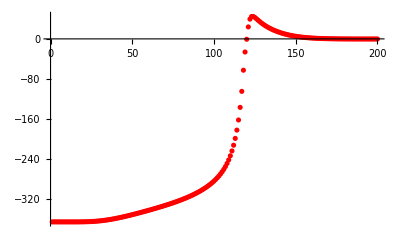

```mathematica
Show[ListPlot[mdiffmuB591,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591=FindMaximum[Interpolation[mdiffmuB591][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591=T/.FindMaximum[Interpolation[mdiffmuB591][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591=FindMinimum[Interpolation[TtomSigmamuB591][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591=T/.FindMinimum[Interpolation[TtomSigmamuB591][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591=Interpolation[TtomPionmuB591][T]-Interpolation[TtomSigmamuB591][T]/.{T-> TmSigmaMinmuB591};
```

```mathematica
mSigmamuB591d5data=Flatten[Import["./muB/muB591d5/mSigma.dat"]];
```

```mathematica
mPionmuB591d5data=Flatten[Import["./muB/muB591d5/mPion.dat"]];
```

```mathematica
TtomSigmamuB591d5=Table[{Tdata[[i]],mSigmamuB591d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591d5=Table[{Tdata[[i]],mPionmuB591d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591d5=Table[{Tdata[[i]],mPionmuB591d5data[[i]]-mSigmamuB591d5data[[i]]},{i,1,Length[Tdata]}];
```

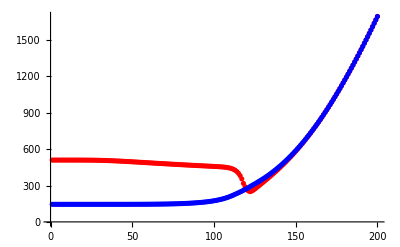

```mathematica
Show[ListPlot[TtomSigmamuB591d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

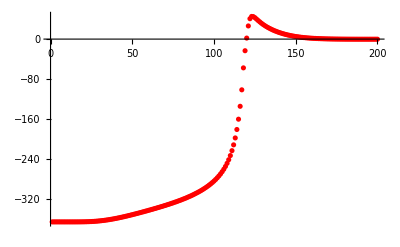

```mathematica
Show[ListPlot[mdiffmuB591d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591d5=FindMaximum[Interpolation[mdiffmuB591d5][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591d5=T/.FindMaximum[Interpolation[mdiffmuB591d5][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591d5=FindMinimum[Interpolation[TtomSigmamuB591d5][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591d5=T/.FindMinimum[Interpolation[TtomSigmamuB591d5][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591d5=Interpolation[TtomPionmuB591d5][T]-Interpolation[TtomSigmamuB591d5][T]/.{T-> TmSigmaMinmuB591d5};
```

```mathematica
mSigmamuB592data=Flatten[Import["./muB/muB592/mSigma.dat"]];
```

```mathematica
mPionmuB592data=Flatten[Import["./muB/muB592/mPion.dat"]];
```

```mathematica
TtomSigmamuB592=Table[{Tdata[[i]],mSigmamuB592data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB592=Table[{Tdata[[i]],mPionmuB592data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB592=Table[{Tdata[[i]],mPionmuB592data[[i]]-mSigmamuB592data[[i]]},{i,1,Length[Tdata]}];
```

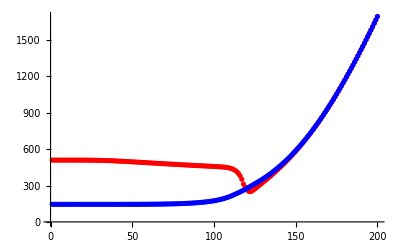

```mathematica
Show[ListPlot[TtomSigmamuB592,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB592,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

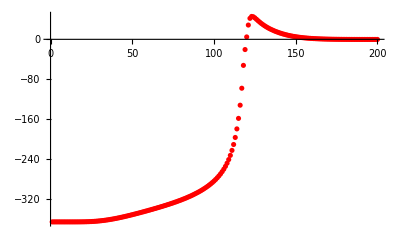

```mathematica
Show[ListPlot[mdiffmuB592,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB592=FindMaximum[Interpolation[mdiffmuB592][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB592=T/.FindMaximum[Interpolation[mdiffmuB592][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB592=FindMinimum[Interpolation[TtomSigmamuB592][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB592=T/.FindMinimum[Interpolation[TtomSigmamuB592][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB592=Interpolation[TtomPionmuB592][T]-Interpolation[TtomSigmamuB592][T]/.{T-> TmSigmaMinmuB592};
```

```mathematica
mSigmamuB592d5data=Flatten[Import["./muB/muB592d5/mSigma.dat"]];
```

```mathematica
mPionmuB592d5data=Flatten[Import["./muB/muB592d5/mPion.dat"]];
```

```mathematica
TtomSigmamuB592d5=Table[{Tdata[[i]],mSigmamuB592d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB592d5=Table[{Tdata[[i]],mPionmuB592d5data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB592d5=Table[{Tdata[[i]],mPionmuB592d5data[[i]]-mSigmamuB592d5data[[i]]},{i,1,Length[Tdata]}];
```

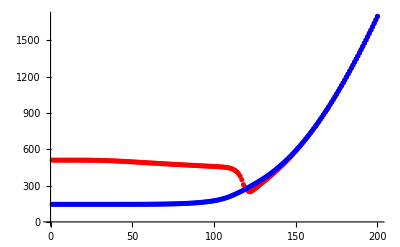

```mathematica
Show[ListPlot[TtomSigmamuB592d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB592d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

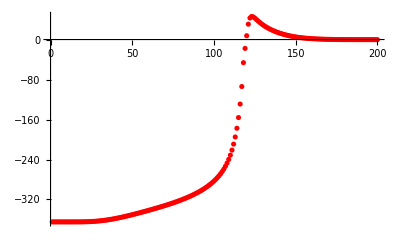

```mathematica
Show[ListPlot[mdiffmuB592d5,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB592d5=FindMaximum[Interpolation[mdiffmuB592d5][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB592d5=T/.FindMaximum[Interpolation[mdiffmuB592d5][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB592d5=FindMinimum[Interpolation[TtomSigmamuB592d5][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB592d5=T/.FindMinimum[Interpolation[TtomSigmamuB592d5][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB592d5=Interpolation[TtomPionmuB592d5][T]-Interpolation[TtomSigmamuB592d5][T]/.{T-> TmSigmaMinmuB592d5};
```

```mathematica
mSigmamuB593data=Flatten[Import["./muB/muB593/mSigma.dat"]];
```

```mathematica
mPionmuB593data=Flatten[Import["./muB/muB593/mPion.dat"]];
```

```mathematica
TtomSigmamuB593=Table[{Tdata[[i]],mSigmamuB593data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB593=Table[{Tdata[[i]],mPionmuB593data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB593=Table[{Tdata[[i]],mPionmuB593data[[i]]-mSigmamuB593data[[i]]},{i,1,Length[Tdata]}];
```

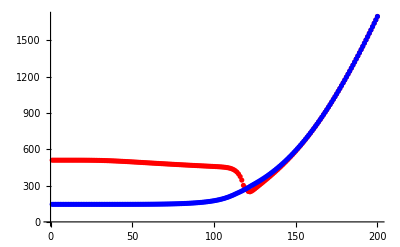

```mathematica
Show[ListPlot[TtomSigmamuB593,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB593,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

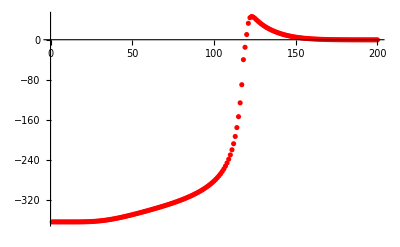

```mathematica
Show[ListPlot[mdiffmuB593,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB593=FindMaximum[Interpolation[mdiffmuB593][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB593=T/.FindMaximum[Interpolation[mdiffmuB593][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB593=FindMinimum[Interpolation[TtomSigmamuB593][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB593=T/.FindMinimum[Interpolation[TtomSigmamuB593][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB593=Interpolation[TtomPionmuB593][T]-Interpolation[TtomSigmamuB593][T]/.{T-> TmSigmaMinmuB593};
```

```mathematica
mSigmamuB591d6data=Flatten[Import["./muB/muB591d6/mSigma.dat"]];
```

```mathematica
mPionmuB591d6data=Flatten[Import["./muB/muB591d6/mPion.dat"]];
```

```mathematica
TtomSigmamuB591d6=Table[{Tdata[[i]],mSigmamuB591d6data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591d6=Table[{Tdata[[i]],mPionmuB591d6data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591d6=Table[{Tdata[[i]],mPionmuB591d6data[[i]]-mSigmamuB591d6data[[i]]},{i,1,Length[Tdata]}];
```

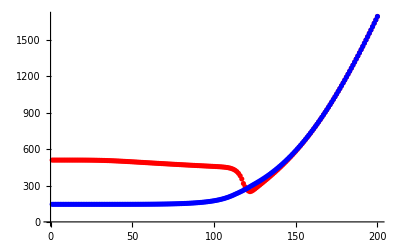

```mathematica
Show[ListPlot[TtomSigmamuB591d6,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591d6,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

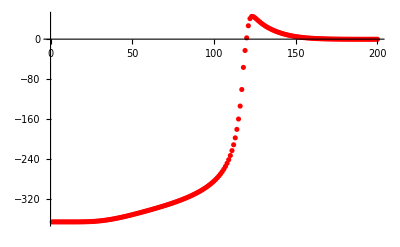

```mathematica
Show[ListPlot[mdiffmuB591d6,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591d6=FindMaximum[Interpolation[mdiffmuB591d6][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591d6=T/.FindMaximum[Interpolation[mdiffmuB591d6][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591d6=FindMinimum[Interpolation[TtomSigmamuB591d6][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591d6=T/.FindMinimum[Interpolation[TtomSigmamuB591d6][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591d6=Interpolation[TtomPionmuB591d6][T]-Interpolation[TtomSigmamuB591d6][T]/.{T-> TmSigmaMinmuB591d6};
```

```mathematica
mSigmamuB591d7data=Flatten[Import["./muB/muB591d7/mSigma.dat"]];
```

```mathematica
mPionmuB591d7data=Flatten[Import["./muB/muB591d7/mPion.dat"]];
```

```mathematica
TtomSigmamuB591d7=Table[{Tdata[[i]],mSigmamuB591d7data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591d7=Table[{Tdata[[i]],mPionmuB591d7data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591d7=Table[{Tdata[[i]],mPionmuB591d7data[[i]]-mSigmamuB591d7data[[i]]},{i,1,Length[Tdata]}];
```

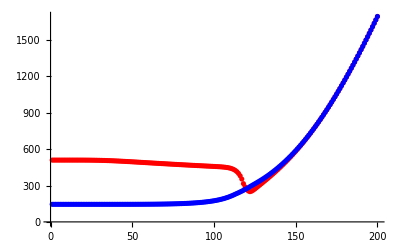

```mathematica
Show[ListPlot[TtomSigmamuB591d7,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591d7,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

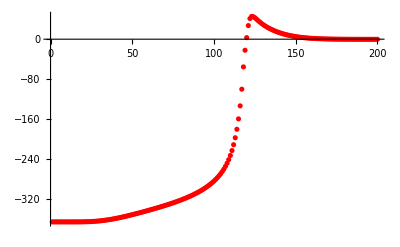

```mathematica
Show[ListPlot[mdiffmuB591d7,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591d7=FindMaximum[Interpolation[mdiffmuB591d7][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591d7=T/.FindMaximum[Interpolation[mdiffmuB591d7][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591d7=FindMinimum[Interpolation[TtomSigmamuB591d7][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591d7=T/.FindMinimum[Interpolation[TtomSigmamuB591d7][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591d7=Interpolation[TtomPionmuB591d7][T]-Interpolation[TtomSigmamuB591d7][T]/.{T-> TmSigmaMinmuB591d7};
```

```mathematica
mSigmamuB591d8data=Flatten[Import["./muB/muB591d8/mSigma.dat"]];
```

```mathematica
mPionmuB591d8data=Flatten[Import["./muB/muB591d8/mPion.dat"]];
```

```mathematica
TtomSigmamuB591d8=Table[{Tdata[[i]],mSigmamuB591d8data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591d8=Table[{Tdata[[i]],mPionmuB591d8data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591d8=Table[{Tdata[[i]],mPionmuB591d8data[[i]]-mSigmamuB591d8data[[i]]},{i,1,Length[Tdata]}];
```

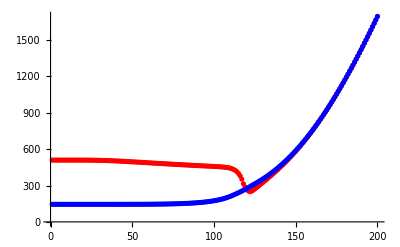

```mathematica
Show[ListPlot[TtomSigmamuB591d8,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591d8,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

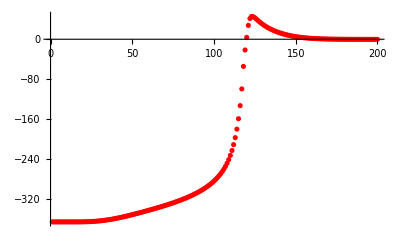

```mathematica
Show[ListPlot[mdiffmuB591d8,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591d8=FindMaximum[Interpolation[mdiffmuB591d8][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591d8=T/.FindMaximum[Interpolation[mdiffmuB591d8][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591d8=FindMinimum[Interpolation[TtomSigmamuB591d8][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591d8=T/.FindMinimum[Interpolation[TtomSigmamuB591d8][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591d8=Interpolation[TtomPionmuB591d8][T]-Interpolation[TtomSigmamuB591d8][T]/.{T-> TmSigmaMinmuB591d8};
```

```mathematica
mSigmamuB591d9data=Flatten[Import["./muB/muB591d9/mSigma.dat"]];
```

```mathematica
mPionmuB591d9data=Flatten[Import["./muB/muB591d9/mPion.dat"]];
```

```mathematica
TtomSigmamuB591d9=Table[{Tdata[[i]],mSigmamuB591d9data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB591d9=Table[{Tdata[[i]],mPionmuB591d9data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB591d9=Table[{Tdata[[i]],mPionmuB591d9data[[i]]-mSigmamuB591d9data[[i]]},{i,1,Length[Tdata]}];
```

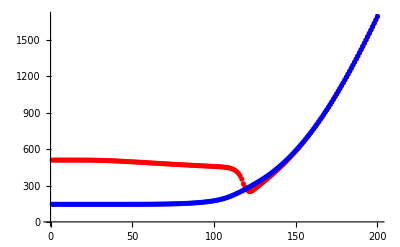

```mathematica
Show[ListPlot[TtomSigmamuB591d9,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB591d9,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

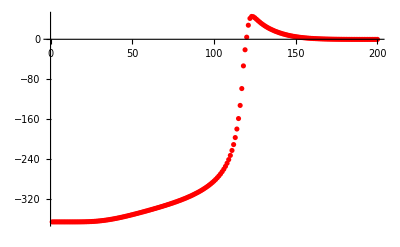

```mathematica
Show[ListPlot[mdiffmuB591d9,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB591d9=FindMaximum[Interpolation[mdiffmuB591d9][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB591d9=T/.FindMaximum[Interpolation[mdiffmuB591d9][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB591d9=FindMinimum[Interpolation[TtomSigmamuB591d9][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB591d9=T/.FindMinimum[Interpolation[TtomSigmamuB591d9][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB591d9=Interpolation[TtomPionmuB591d9][T]-Interpolation[TtomSigmamuB591d9][T]/.{T-> TmSigmaMinmuB591d9};
```

```mathematica
mSigmamuB592d1data=Flatten[Import["./muB/muB592d1/mSigma.dat"]];
```

```mathematica
mPionmuB592d1data=Flatten[Import["./muB/muB592d1/mPion.dat"]];
```

```mathematica
TtomSigmamuB592d1=Table[{Tdata[[i]],mSigmamuB592d1data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB592d1=Table[{Tdata[[i]],mPionmuB592d1data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB592d1=Table[{Tdata[[i]],mPionmuB592d1data[[i]]-mSigmamuB592d1data[[i]]},{i,1,Length[Tdata]}];
```

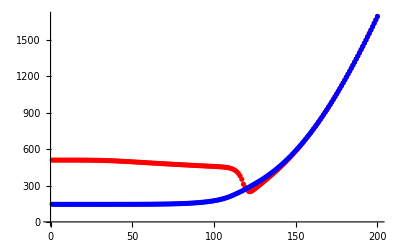

```mathematica
Show[ListPlot[TtomSigmamuB592d1,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB592d1,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

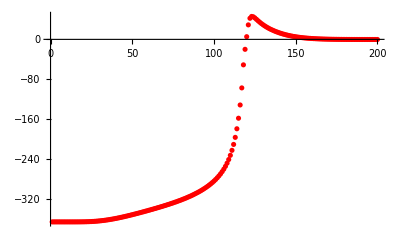

```mathematica
Show[ListPlot[mdiffmuB592d1,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB592d1=FindMaximum[Interpolation[mdiffmuB592d1][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB592d1=T/.FindMaximum[Interpolation[mdiffmuB592d1][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB592d1=FindMinimum[Interpolation[TtomSigmamuB592d1][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB592d1=T/.FindMinimum[Interpolation[TtomSigmamuB592d1][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB592d1=Interpolation[TtomPionmuB592d1][T]-Interpolation[TtomSigmamuB592d1][T]/.{T-> TmSigmaMinmuB592d1};
```

```mathematica
mSigmamuB592d2data=Flatten[Import["./muB/muB592d2/mSigma.dat"]];
```

```mathematica
mPionmuB592d2data=Flatten[Import["./muB/muB592d2/mPion.dat"]];
```

```mathematica
TtomSigmamuB592d2=Table[{Tdata[[i]],mSigmamuB592d2data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
TtomPionmuB592d2=Table[{Tdata[[i]],mPionmuB592d2data[[i]]},{i,1,Length[Tdata]}];
```

```mathematica
mdiffmuB592d2=Table[{Tdata[[i]],mPionmuB592d2data[[i]]-mSigmamuB592d2data[[i]]},{i,1,Length[Tdata]}];
```

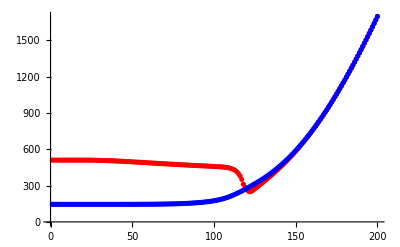

```mathematica
Show[ListPlot[TtomSigmamuB592d2,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[TtomPionmuB592d2,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

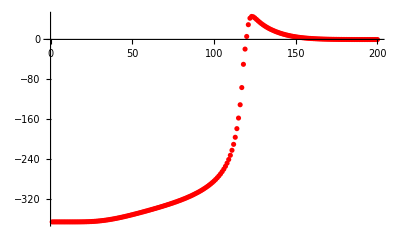

```mathematica
Show[ListPlot[mdiffmuB592d2,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
mdiffMaxmuB592d2=FindMaximum[Interpolation[mdiffmuB592d2][T],{T,115,140}][[1]];
```

```mathematica
TmdiffMaxmuB592d2=T/.FindMaximum[Interpolation[mdiffmuB592d2][T],{T,115,140}][[2]];
```

```mathematica
mSigmaMinmuB592d2=FindMinimum[Interpolation[TtomSigmamuB592d2][T],{T,115,140}][[1]];
```

```mathematica
TmSigmaMinmuB592d2=T/.FindMinimum[Interpolation[TtomSigmamuB592d2][T],{T,115,140}][[2]];
```

```mathematica
mdiffTmSigmaMinmuB592d2=Interpolation[TtomPionmuB592d2][T]-Interpolation[TtomSigmamuB592d2][T]/.{T-> TmSigmaMinmuB592d2};
```

```mathematica
muBtomdiffTmSigmaMin={{560,mdiffTmSigmaMinmuB560},{570,mdiffTmSigmaMinmuB570},{580,mdiffTmSigmaMinmuB580},{590,mdiffTmSigmaMinmuB590},{590.5,mdiffTmSigmaMinmuB590d5},{591,mdiffTmSigmaMinmuB591},{591.5,mdiffTmSigmaMinmuB591d5},{591.6,mdiffTmSigmaMinmuB591d6},{591.7,mdiffTmSigmaMinmuB591d7},{591.8,mdiffTmSigmaMinmuB591d8},{591.9,mdiffTmSigmaMinmuB591d9},{592,mdiffTmSigmaMinmuB592},{592.1,mdiffTmSigmaMinmuB592d1},{592.2,mdiffTmSigmaMinmuB592d2},{592.5,mdiffTmSigmaMinmuB592d5},{593,mdiffTmSigmaMinmuB593}};
```

```mathematica
muBtomdiffTmSigmaMin2={{590,mdiffTmSigmaMinmuB590},{590.5,mdiffTmSigmaMinmuB590d5},{591,mdiffTmSigmaMinmuB591},{591.5,mdiffTmSigmaMinmuB591d5},{591.6,mdiffTmSigmaMinmuB591d6},{591.7,mdiffTmSigmaMinmuB591d7},{591.8,mdiffTmSigmaMinmuB591d8},{591.9,mdiffTmSigmaMinmuB591d9},{592,mdiffTmSigmaMinmuB592},{592.1,mdiffTmSigmaMinmuB592d1},{592.2,mdiffTmSigmaMinmuB592d2},{592.5,mdiffTmSigmaMinmuB592d5},{593,mdiffTmSigmaMinmuB593}};
```

```mathematica
muBtomdiffMax={{560,mdiffMaxmuB560},{570,mdiffMaxmuB570},{580,mdiffMaxmuB580},{590,mdiffMaxmuB590},{590.5,mdiffMaxmuB590d5},{591,mdiffMaxmuB591},{591.5,mdiffMaxmuB591d5},{592,mdiffMaxmuB592},{592.5,mdiffMaxmuB592d5},{593,mdiffMaxmuB593}};
```

```mathematica
muBtomdiffMax2={{590,mdiffMaxmuB590},{590.5,mdiffMaxmuB590d5},{591,mdiffMaxmuB591},{591.5,mdiffMaxmuB591d5},{592,mdiffMaxmuB592},{592.5,mdiffMaxmuB592d5},{593,mdiffMaxmuB593}};
```

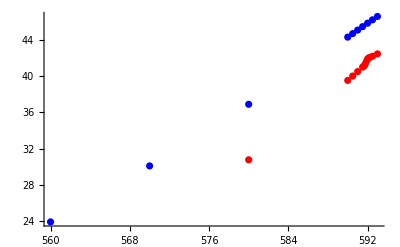

```mathematica
Show[ListPlot[muBtomdiffMax,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtomdiffTmSigmaMin,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

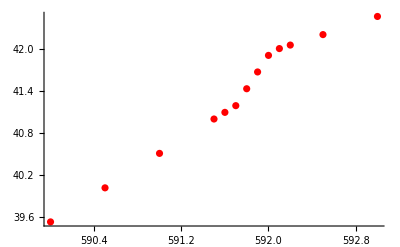

```mathematica
Show[ListPlot[muBtomdiffTmSigmaMin2,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
muBtomdiffTmSigmaMin3=Drop[muBtomdiffTmSigmaMin2,-4]
```

{{590,39.5364},{590.5,40.0224},{591,40.5142},{591.5,41.0048},{591.6,41.0996},{591.7,41.1953},{591.8,41.4368},{591.9,41.6763},{592,41.9127}}

```mathematica
muBtomdiffPoly[x_]=Fit[muBtomdiffTmSigmaMin3,  {1,x^1,x^2,x^3},x];
```

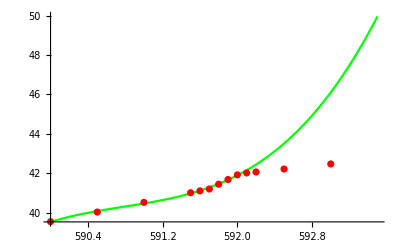

```mathematica
Show[Plot[muBtomdiffPoly[x],{x,590,593.5},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],ListPlot[muBtomdiffTmSigmaMin2,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```